```mathematica
p0[e_,s_]:=Integrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π},Assumptions->{Element[e,Reals], e>0}]
```

```mathematica
np0[e_,s_]:=NIntegrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π}]
```

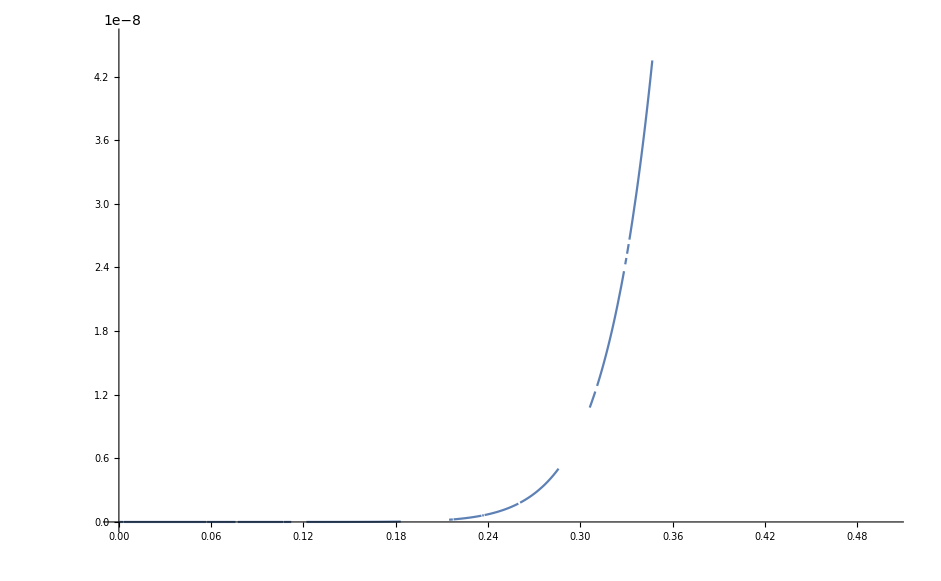

```mathematica
Plot[{3 π e-(9 π e^3)/8+(9 π e^5)/64-(19 π e^7)/3072-(133 π e^9)/81920-np0[e,1]*(1-e^2)^(3/2)}, {e, 0, 0.5}]
```

```mathematica
3 π e-(9 π e^3)/8+(9 π e^5)/64-(19 π e^7)/3072-(133 π e^9)/81920-np0[e,1]*(1-e^2)^(3/2)/.e->0.5
```

NIntegrate::inumr: The integrand ⅇ^(ⅈ (u-e Sin[u]))/(1-e Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

2.73295×10^-6-2.88444×10^-16 ⅈ

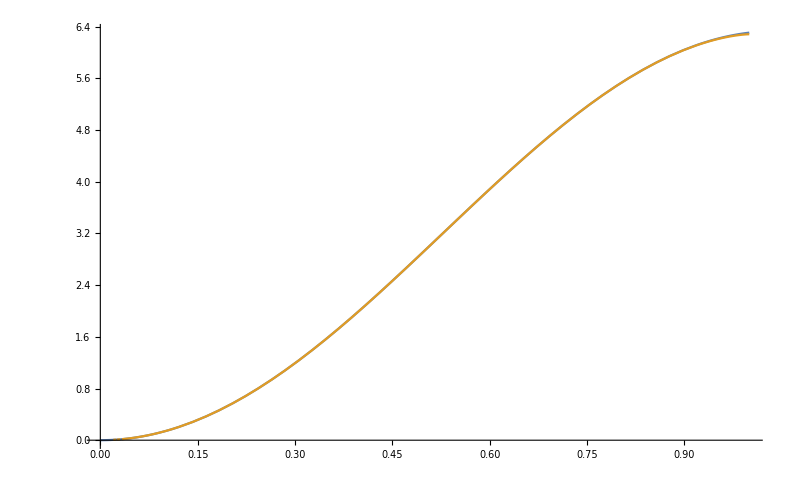

```mathematica
Plot[{(9 π e^2)/2-(13 π e^4)/4+(27 π e^6)/32-(29 π e^8)/320+(67 π e^10)/11520-(299 π e^12)/268800,np0[e,2]*(1-e^2)^(3/2)},{e,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

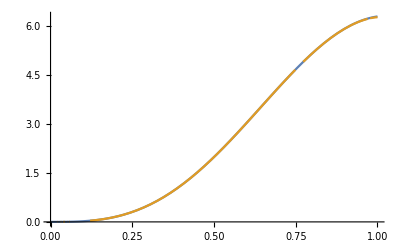

```mathematica
Plot[{(53 π e^3)/8-(879 π e^5)/128+(13893 π e^7)/5120-(21359 π e^9)/40960+(41067 π e^11)/655360-(3547143 π e^13)/734003200,np0[e,3]*(1-e^2)^(3/2)},{e,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.1269×10^-7}. NIntegrate obtained -6.55725×10^-16+8.32667×10^-17 ⅈ and 1.50746×10^-12 for the integral and error estimates.

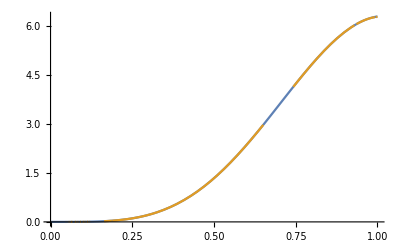

```mathematica
Plot[{(77 π e^4)/8-(513 π e^6)/40+(2179 π e^8)/320-(19157 π e^10)/10080+(71857 π e^12)/215040-(41663 π e^14)/1075200,np0[e,4]*(1-e^2)^(3/2)},{e,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained -6.40113×10^-16-3.60822×10^-16 ⅈ and 1.68626×10^-12 for the integral and error estimates.

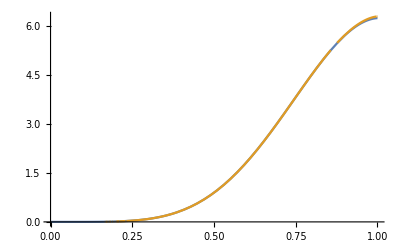

```mathematica
Plot[{(1773 π e^5)/128-(68815 π e^7)/3072+(855815 π e^9)/57344-(30103445 π e^11)/5505024+(3055138525 π e^13)/2378170368-(438397391 π e^15)/2113929216,np0[e,5]*(1-e^2)^(3/2)},{e,0,1}]
```

```mathematica
np0[e,1]*(1-e^2)^(3/2)
```

NIntegrate::inumr: The integrand ⅇ^(ⅈ (u-e Sin[u]))/(1-e Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

(1-e^2)^(3/2) NIntegrate[Exp[ⅈ (u-e Sin[u])]/(1-e Cos[u])^2,{u,0,2 π}]

```mathematica
D[(1-e)^(-3/2), {e,n}]
```

(-1)^n (1-e)^(-3/2-n) FactorialPower[-3/2,n]

```mathematica
Series[(1-e)^(-3/2), {e,0,10}]
```

1+(3 e)/2+(15 e^2)/8+(35 e^3)/16+(315 e^4)/128+(693 e^5)/256+(3003 e^6)/1024+(6435 e^7)/2048+(109395 e^8)/32768+(230945 e^9)/65536+(969969 e^10)/262144+O[e]^11

```mathematica
divergenceless[e_,s_]:=Integrate[Exp[I*s*(u-e*Sin[u])]*(1-e^2)^(3/2)/(1-e*Cos[u])^2, {u, 0, 2π},Assumptions->{Element[e,Reals], e>0,e<1}]
```

```mathematica
integrand[e_,s_]:=Exp[I*s*(u-e*Sin[u])]*(1-e^2)^(3/2)/(1-e*Cos[u])^2
```

```mathematica
Series[divergenceless[e,1],{e,1,5},Assumptions->e<1]
```

Integrate::idiv: Integral of (2 √2 (1-e)^(3/2) ⅇ^(ⅈ u-ⅈ Sin[u]))/(-1+Cos[u])^2-(ⅈ (1-e)^(3/2) (-1+e) ⅇ^(«1») (-3 ⅈ-5 ⅈ Cos[u]-4 Sin[u]+4 Cos[u] Sin[u]))/(√2 (-1+Cos[u])^3)-((1-e)^(3/2) ((«1»«1»)^2 «1» («1»))/(8 √2 (-1+«1»)^4)+((1-e)^(3/2) (-1+e)^3 ⅇ^(«1») (3-81 Cos[u]-711 Cos[u]^2-747 Cos[u]^3+«13»+192 ⅈ Cos[u] Sin[u]^3-192 ⅈ Cos[u]^2 Sin[u]^3+64 ⅈ Cos[u]^3 Sin[u]^3))/(96 √2 (-1+Cos[u])^5) does not converge on {0,2 π}.

$Aborted

```mathematica
Limit[Integrate[FullSimplify[D[integrand[e, 1],{e,2}],Assumptions->{Element[e,Reals], e>0,e<1}],{u,0,2π}],e->1,Direction->"FromBelow"]
```

$Aborted

```mathematica
Integrate[Limit[D[integrand[1-e,1],{e,2}],e->0,Direction->"FromAbove"],{u,0,2π}]
```

Integrate::idiv: Integral of DirectedInfinity[ⅇ^(ⅈ Re[u-Sin[u]])] does not converge on {0,2 π}.

∫_0^(2 π) DirectedInfinity[ⅇ^(ⅈ Re[u-Sin[u]])/Sign[-1+Cos[u]]^2]ⅆu

```mathematica
N[Integrate[(ⅇ^(ⅈ Re[u-Sin[u]]) Sign[Sin[u/2]]^4)/Sign[1-Cos[u]]^4,{u,0,2π}]]
```

2.76492

```mathematica
Column[Table[Print[Subscript[p, 0,s],":  " ,Series[divergenceless[e,s],{e,1,10+s},Assumptions->e<1]], {s,0,10}]]
```

p_(0,0):  2 π

p_(0,1):  Series[Integrate[((1-e^2)^(3/2) ⅇ^(ⅈ (u-e Sin[u])))/(1-e Cos[u])^2,{u,0,2 π},Assumptions→{e∈ℝ,e>0,e<1}],{e,1,11}]

p_(0,2):  Series[Integrate[((1-e^2)^(3/2) ⅇ^(2 ⅈ (u-e Sin[u])))/(1-e Cos[u])^2,{u,0,2 π},Assumptions→{e∈ℝ,e>0,e<1}],{e,1,12}]

p_(0,3):  Series[Integrate[((1-e^2)^(3/2) ⅇ^(3 ⅈ (u-e Sin[u])))/(1-e Cos[u])^2,{u,0,2 π},Assumptions→{e∈ℝ,e>0,e<1}],{e,1,13}]

$Aborted